# NarvAC

### Author: Carlos Manuel Rodríguez Martínez Email: fis.carlosmanuel@gmail.com

A turing-complete register and stack based machine implemented in logical gates.

## Auxiliary

Definitions to simulate the behavior or looped circuits. MemoryEvaluate evaluates a function with the argument of the previous result. Each MemoryEvaluate function is distinguished by a tag.

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Packages","AdvancedMapping.wl"}]]
HalfSplit[l_]:=TakeDrop[l, Floor[Length[l]/2]];

SetAttributes[MemoryEvaluate,HoldAll];
MemoryEvaluate[expr_,tag_]:=Block[{},
If[Head[MemorySymbol[tag]]== MemorySymbol,
MemorySymbol[tag] = 0;
];
MemorySymbol[tag] = ReleaseHold[expr[MemorySymbol[tag]]];
Return[MemorySymbol[tag]];
];

Unprotect[BitAnd];
BitAnd[1,x_]:=x;
BitAnd[x_,1]:=x;
Protect[BitAnd];

Unprotect[BitNot];
BitNot[0] := 1;
BitNot[1] := 0;
Protect[BitAnd];

DecimalToBinary[n_,size_ :8]:=PadLeft[IntegerDigits[n,2],size];
BinaryToDecimal[l_]:=FromDigits[l,2];
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

### Examples

Example of use

```mathematica
MemoryEvaluate[f,"Example"]
```

f[0]

```mathematica
MemoryEvaluate[f,"Example"]
```

f[f[0]]

```mathematica
MemoryEvaluate[f,"Example"]
```

f[f[f[0]]]

## Visualization

### Circuit result tables

Tables of input-output for simple circuits.

```mathematica
VisualizeGate[module_] := Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,{Apply[module,#]}]&,Tuples[{0,1},2]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],2],{"Result"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];
VisualizeAdder[module_,inputSize_,flagName_] := Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,Apply[module,#]]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{flagName,"Result"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];

VisualizeMultiplexer[mux_,inputSize_]:=Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,{mux[#,Take[Alphabet[],2^inputSize]]}]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{"Selection"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];
```

```mathematica
VisualizeGate[BitAnd]
```

A | B | Result
0 | 0 | 0
0 | 1 | 0
1 | 0 | 0
1 | 1 | 1

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

```mathematica
VisualizeMultiplexer[Mux4to1,2]
```

A | B | Selection
0 | 0 | a
0 | 1 | b
1 | 0 | c
1 | 1 | d

### Tree structure of expression

There are two ways to represent an expression as a graph. First by drawing the expression as a tree form, for example:

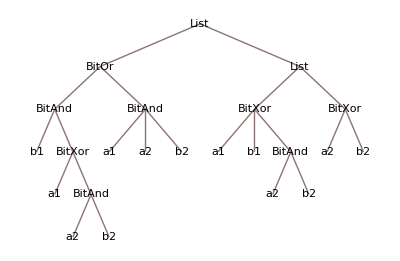

```mathematica
TreeForm[ALUAdder[{a1,a2},{b1,b2}]]
```

or by transforming the tree in a more compact form by removing the redundancy of repeated variables, for example:

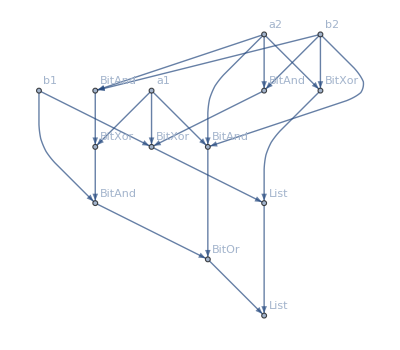

```mathematica
CompactTreeForm[ALUAdder[{a1,a2},{b1,b2}]]
```

The simple TreeForm has the disadvantage of quickly being unpractical with complex expressions. The function
PlotExpression[expr, opts] offers a more visible representation of a TreeForm for large expressions and
PlotInteractiveSystem[system] plots an interactive TreeForm representation of the circuit.
Analogously,
CompactTreeForm[system] plots an expression as a graph and
PlotCompactInteractiveSystem[system] plots an interactive graph of the circuit.
An adjacency matrix representation of the circuit is provided by
CompactExprMatrixPlot[system]

### Evaluation of expression heads

```mathematica
EvaluateHead[expr_,values_]:=ReplaceRepeated[expr,{f_Symbol[arg__]:>ReplaceAll[f[arg],values][arg]}];

StructuredEvaluateHead[expr_,values_]:=Block[{logicOp},
logicOp = {BitOr,BitAnd,BitXor,BitNot};ReplaceRepeated[expr,{f_Symbol[arg__]/;MemberQ[logicOp,f]:>{f,ReplaceAll[f[arg],values]}[arg]}]
];
```

```mathematica
NestedEvaluate[expr_,values_]:=If[Head[expr]===List,
Map[NestedEvaluate[#,values]&,Level[expr,1]],
ReplaceAll[EvaluateHead[expr,values],values]
];

StructuredNestedEvaluate[expr_,values_]:=If[Head[expr]===List,
Map[StructuredNestedEvaluate[#,values]&,Level[expr,1]],
ReplaceAll[StructuredEvaluateHead[expr,values],values]
];
```

#### Examples

```mathematica
expr = ALUAdder[{a1,a2},{b1,b2}]
```

{BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]],{BitXor[a1,b1,BitAnd[a2,b2]],BitXor[a2,b2]}}

```mathematica
NestedEvaluate[expr,{a1->0,a2->1,b1->0,b2->1}]
```

{0[0[0,1[0,1[1,1]]],0[0,1,1]],{1[0,0,1[1,1]],0[1,1]}}

### Tree graph

```mathematica
GetSymbols[system_]:=Complement[
DeleteDuplicates[Level[system,{-1},Heads->True]],
{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association}
];
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];
EvaluateLists[edges_,labels_,pos_]:=Block[{children,listValue},
children = Cases[edges,pos->x_:>x];
listValue = Cases[labels,HoldPattern[x_/;MemberQ[children,x]->_]][[All,2]];
labels/.(pos->List)->(pos->listValue)
];

TreeFormToGraph[treeForm_]:=Module[
{graph,tree=ToExpression@ToBoxes@treeForm,order,pos,label,listPositions,edges,evaluatedLists},
label=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity];
listPositions = Reverse[Cases[label,HoldPattern[x_->List]:>x]];
{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
edges = DirectedEdge@@@order;
evaluatedLists = Part[Fold[EvaluateLists[edges,#1,#2]&,label,listPositions],Reverse[listPositions]];
graph = Graph[edges,VertexLabels->label,VertexCoordinates->MapIndexed[Rule[First[#2],#]&,pos]];
{graph,ReleaseHold[label],evaluatedLists}
];

RuleListToMatrix[list_]:=Transpose[{list[[All,1]],list[[All,2]]}];
SeparateFirst[l_]:={First[l],Drop[l,1]};
MakeReplaceRules[fixed_,toBeReplaced_]:=Map[(vertex_->#):>(vertex->fixed)&,toBeReplaced];

ReplaceRuleForLabel[labels_,labelName_]:=Block[{fixed,toBeReplaced,replaceRules},
{fixed,toBeReplaced}=SeparateFirst[Cases[RuleListToMatrix[labels],{vertex_,labelName}:>vertex]];
replaceRules = MakeReplaceRules[fixed,toBeReplaced];
MakeReplaceRules[fixed,toBeReplaced]
];
ReplaceRuleForAllLabels[labels_]:=Block[{nameLabels},
nameLabels = DeleteCases[
DeleteDuplicates[labels[[All,2]]],
x_ /;MemberQ[{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association},x]
];
Flatten[Map[ReplaceRuleForLabel[labels,#]&,nameLabels]]
];

Options[CompactTreeForm]=Join[{"ShowLabels"->Automatic},Options[Graph]];
CompactTreeForm[expr_,opts: OptionsPattern[]]:=Block[{graph,labels,newGraph,deleteVertex,newLabels},
{graph,labels} = Take[TreeFormToGraph[TreeForm[expr]],2];
newGraph = ReplaceAll[EdgeList[graph],ReplaceRuleForAllLabels[labels]];
deleteVertex = Complement[labels[[All,1]],VertexList[newGraph]];
newLabels = DeleteCases[labels,x_/;MemberQ[deleteVertex,First[x]]];

Graph[
ReplaceAll[newGraph,x_->y_:>y->x],
If[OptionValue["ShowLabels"]===Automatic,
VertexLabels->newLabels,
VertexLabels->None
],
DirectedEdges->True,
FilterRules[{opts},Options[Graph]]
]
];
```

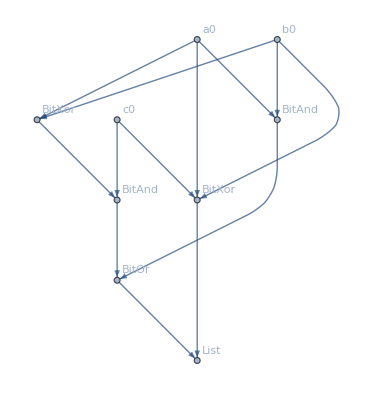

```mathematica
CompactTreeForm[FullAdder[a0,b0,c0]]
```

```mathematica
DecorateVertexes[labels_]:=Block[{and,xor,or,not,list,true,false},
and = Map[Style[#,RGBColor[0., 0.96, 0.8300000000000001]]&,Cases[labels,HoldPattern[x_->BitAnd]:>x]];
xor = Map[Style[#,RGBColor[0.86, 0.02, 0.]]&,Cases[labels,HoldPattern[x_->BitXor]:>x]];
or = Map[Style[#,RGBColor[0.26, 0.39, 1.]]&,Cases[labels,HoldPattern[x_->BitOr]:>x]];
not = Map[Style[#,RGBColor[1., 1., 0.04]]&,Cases[labels,HoldPattern[x_->BitNot]:>x]];
list = Map[Style[#,RGBColor[0.86, 0., 0.8200000000000001]]&,Cases[labels,HoldPattern[x_->List]:>x]];
true = Map[Style[#,RGBColor[0.12, 0.84, 0.]]&,Cases[labels,HoldPattern[x_->1]:>x]];
false = Map[Style[#,RGBColor[0.16, 0.02, 0.]]&,Cases[labels,HoldPattern[x_->0]:>x]];

Join[and,xor,or,not,list,true,false]
];
MakeRuleForListValue[listValue_]:=(First[listValue]->List)->(listValue);
FormatLabels[labels_]:=MapAt[ToString,labels,{All,2}];

Options[CompactHighlightedTreeForm]=Join[{"ShowLabels"->Automatic},Options[Graph]];
CompactHighlightedTreeForm[expr_,opts: OptionsPattern[]]:=Block[
{
graph,labels,listValues,newGraph,deleteVertex,newLabels,
evaluatedGraph,evaluatedLabels,newEvaluatedGraph,deleteEvaluatedVertex,newEvaluatedLabels,
highlightedVertexes,
},
{graph,labels} = Take[TreeFormToGraph[TreeForm[expr]],2];
newGraph = ReplaceAll[EdgeList[graph],ReplaceRuleForAllLabels[labels]];
deleteVertex = Complement[labels[[All,1]],VertexList[newGraph]];
newLabels = DeleteCases[labels,x_/;MemberQ[deleteVertex,First[x]]];

{evaluatedGraph,evaluatedLabels,listValues} = TreeFormToGraph[TreeForm[expr]];
newEvaluatedGraph = ReplaceAll[EdgeList[evaluatedGraph],ReplaceRuleForAllLabels[evaluatedLabels]];
deleteEvaluatedVertex = Complement[evaluatedLabels[[All,1]],VertexList[newEvaluatedGraph]];
newEvaluatedLabels = DeleteCases[evaluatedLabels,x_/;MemberQ[deleteEvaluatedVertex,First[x]]];

highlightedVertexes = Cases[newEvaluatedLabels,HoldPattern[x_->1]:>x];

graph = Graph[
ReplaceAll[newGraph,x_->y_:>y->x],
If[OptionValue["ShowLabels"]===Automatic,
VertexLabels->FormatLabels[newLabels/.Map[MakeRuleForListValue,listValues]],
VertexLabels->None
],
DirectedEdges->True,
ImageSize->500,
FilterRules[{opts},Options[Graph]]
];
GraphPlot[
HighlightGraph[
ReplaceAll[graph,x_->y_:>y->x],
DecorateVertexes[labels],
VertexSize->0.2,
FilterRules[{opts},Options[HighlightGraph]]
]
]
];

Options[CompactEvaluatedTreeForm]=Join[{"ShowLabels"->Automatic},Options[Graph]];
CompactEvaluatedTreeForm[expr_,values_,opts: OptionsPattern[]]:=Block[
{
graph,labels,listValues,newGraph,deleteVertex,newLabels,
evaluatedGraph,evaluatedLabels,newEvaluatedGraph,deleteEvaluatedVertex,newEvaluatedLabels,
highlightedVertexes,highlightedEdges
},
{graph,labels} = Take[TreeFormToGraph[TreeForm[expr]],2];
newGraph = ReplaceAll[EdgeList[graph],ReplaceRuleForAllLabels[labels]];
deleteVertex = Complement[labels[[All,1]],VertexList[newGraph]];
newLabels = DeleteCases[labels,x_/;MemberQ[deleteVertex,First[x]]];

{evaluatedGraph,evaluatedLabels,listValues} = TreeFormToGraph[TreeForm[NestedEvaluate[expr,values]]];
newEvaluatedGraph = ReplaceAll[EdgeList[evaluatedGraph],ReplaceRuleForAllLabels[evaluatedLabels]];
deleteEvaluatedVertex = Complement[evaluatedLabels[[All,1]],VertexList[newEvaluatedGraph]];
newEvaluatedLabels = DeleteCases[evaluatedLabels,x_/;MemberQ[deleteEvaluatedVertex,First[x]]];

highlightedVertexes = Cases[newEvaluatedLabels,HoldPattern[x_->1]:>x];
highlightedEdges = Select[EdgeList[newGraph],MemberQ[highlightedVertexes,Last[#]]&];
highlightedEdges = Map[Style[#,Green]&,highlightedEdges];

graph = Graph[
ReplaceAll[newGraph,x_->y_:>y->x],
If[OptionValue["ShowLabels"]===Automatic,
VertexLabels->FormatLabels[newLabels/.Map[MakeRuleForListValue,listValues]],
VertexLabels->None
],
DirectedEdges->True,
ImageSize->500,
FilterRules[{opts},Options[Graph]]
];
GraphPlot[
HighlightGraph[
ReplaceAll[graph,x_->y_:>y->x],
Join[ReplaceAll[highlightedEdges,x_->y_:>y->x],DecorateVertexes[labels/.values]],
VertexSize->0.2,
FilterRules[{opts},Options[HighlightGraph]]
]
]
];

BinaryResultToDecimal[n_List /; Depth[n]>2]:=Map[BinaryResultToDecimal,n];
BinaryResultToDecimal[n_List /; Depth[n]==2]:=FromDigits[n,2];
BinaryResultToDecimal[n_]:=n;

PlotCompactInteractiveSystem[system_,opts: OptionsPattern[]]:=DynamicModule[{symbols,controllerSymbols,boxes,controls,gathered},
symbols = GetSymbols[system];
controllerSymbols = Map[Symbol[StringJoin[SymbolName[#],ToString[$ModuleNumber]]]&,symbols];
boxes = Map[Checkbox[Dynamic[#],{0,1}]&,controllerSymbols];
controls = Panel[Multicolumn[Map[Row[{SymbolName[#[[1]]]<>": ",#[[2]]}]&,Transpose[{symbols,boxes}]],5],Style["Input",Bold]];
gathered = GatherBy[symbols,StringTake[SymbolName[#],1]&];

Panel[
Column[
{
controls,
Framed[Row[{Style["Input in decimal: ",Bold],Dynamic[BinaryResultToDecimal[ReplaceAll[gathered,Thread[symbols->controllerSymbols]]]]}]],
Framed[Row[{Style["Result: ",Bold],Dynamic[ReplaceAll[system,Thread[symbols->controllerSymbols]]]}]],
Framed[Row[{Style["Result in decimal: ",Bold],Dynamic[BinaryResultToDecimal[ReplaceAll[system,Thread[symbols->controllerSymbols]]]]}]],
Framed[Dynamic[CompactEvaluatedTreeForm[system,Thread[symbols->controllerSymbols],opts]]]
}
]
]
,
SaveDefinitions->True
];
PlotCompactSystemEvaluations[system_,opts: OptionsPattern[]]:=Block[{symbols,replacements},
symbols = GetSymbols[system];
replacements = Map[symbols->#&,Tuples[{0,1},Length[symbols]]];
ProgressMap[
Panel[
Column[
{
Framed[Row[{Style["Input: ",Bold],Thread[#]}]],
Framed[Row[{Style["Result: ",Bold],ReplaceAll[system,Thread[#]]}]],
Framed[CompactEvaluatedTreeForm[system,Thread[#],opts]]
}
]
]&,
replacements
]
];
```

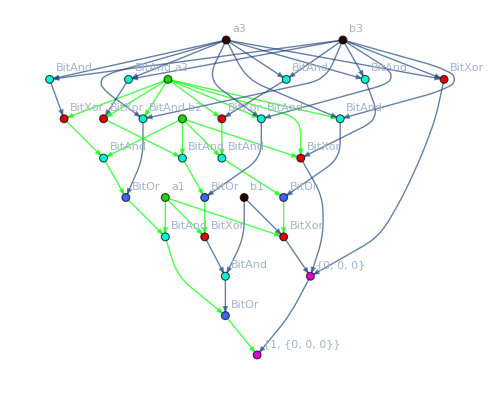

```mathematica
CompactEvaluatedTreeForm[ALUAdder[{a1,a2,a3},{b1,b2,b3}],{a1->1,a2->1,a3->0,b1->0,b2->1,b3->0},EdgeStyle->Thick]
```

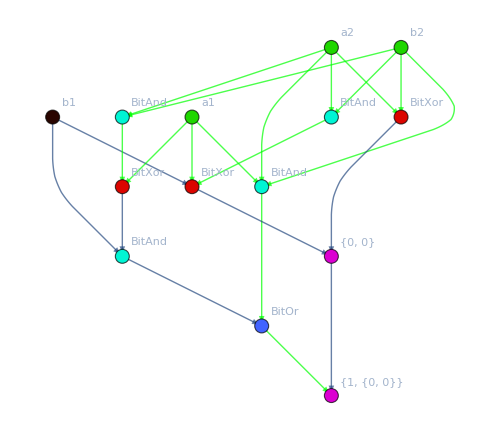

```mathematica
CompactEvaluatedTreeForm[ALUAdder[{a1,a2},{b1,b2}],{a1->1,a2->1,b1->0,b2->1},EdgeStyle->Thick]
```

```mathematica
ListAnimate[PlotCompactSystemEvaluations[ALUAdder[{a1,a2},{b1,b2}],EdgeStyle->Thick]]
```

```mathematica
PlotCompactInteractiveSystem[ALUAdder[{a1,a2,a3},{b1,b2,b3}],EdgeStyle->Thick]
```

## Basic logic gates

```mathematica
Map[
PlotCompactInteractiveSystem[
{#[a,b]},
ImageSize->200,
EdgeStyle->Thick,
VertexLabelStyle->18
]&,
{BitAnd,BitOr,BitXor}
]
```

{,,}

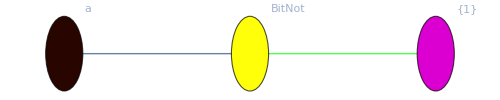
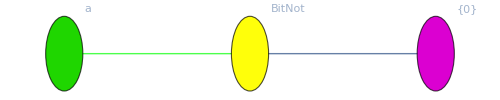
{Input: {a→0}
Result: {1}
-Graphics-,Input: {a→1}
Result: {0}
-Graphics-}

```mathematica
PlotCompactSystemEvaluations[{BitNot[a]},ImageSize->500,EdgeStyle->Thick]
```

```mathematica
PlotCompactInteractiveSystem[{BitNot[a]},ImageSize->500,EdgeStyle->Thick]
```

## Multiplexer

The multiplexer is a device that selects between input signals  {i_0, i_1,... , i_n} and forwards it to a single output line by selecting it with a signal {s_(1,)..., s_m} with m = 2^n.
In the context of this computer, multiplexers are used to select output signals of a circuit, for example, selecting the desired output of the ALU by using an opcode.

-Graphics-

Figure: Schematic of a 2-to-1 Multiplexer. It can be equated to a controlled switch.
Source: https://en.wikipedia.org/wiki/Multiplexer

### 2 to 1

Selects a two input signal  {i_0, i_1} by the 1 bit selector signal {s_1}

-Graphics-

```mathematica
Mux2to1[{select_},{input1_,input2_}]:=BitOr[BitAnd[input1,BitNot[select]],BitAnd[input2,select]];
```

### 4 to 1

Selects a four input signal  {i_0, i_1, i_2, i_3} by a two bit selector {s_0, s_1}.

-Graphics-

```mathematica
Mux4to1[{select1_,select2_},{input1_,input2_,input3_,input4_}]:=Mux2to1[
{select1},
{
Mux2to1[{select2},{input1,input2}],
Mux2to1[{select2},{input3,input4}]
}
];
```

### 8 to 1

Selects a eight input signal  {i_0, i_1, i_2, i_3,i_4, i_5, i_6, i_7}  by a four bit selector {s_0, s_1,s_2, s_3}. It is possible to build a 8:1 multiplexer using two 4:1 multiplexers.

-Graphics-

```mathematica
Mux8to1[{select1_,select2_,select3_},{input1_,input2_,input3_,input4_,input5_,input6_,input7_,input8_}]:=
Mux2to1[
{select1},
{
Mux4to1[{select2,select3},{input1,input2,input3,input4}],
Mux4to1[{select2,select3},{input5,input6,input7,input8}]
}
];
```

### Visualizations

Result

```mathematica
{VisualizeMultiplexer[Mux2to1,1],VisualizeMultiplexer[Mux4to1,2],VisualizeMultiplexer[Mux8to1,3]}
```

{A | Selection
0 | a
1 | b,A | B | Selection
0 | 0 | a
0 | 1 | b
1 | 0 | c
1 | 1 | d,A | B | C | Selection
0 | 0 | 0 | a
0 | 0 | 1 | b
0 | 1 | 0 | c
0 | 1 | 1 | d
1 | 0 | 0 | e
1 | 0 | 1 | f
1 | 1 | 0 | g
1 | 1 | 1 | h}

Mux 2 to 1

```mathematica
Mux2to1[{s},{i1,i2}]
```

BitOr[BitAnd[i1,BitNot[s]],BitAnd[i2,s]]

```mathematica
PlotCompactInteractiveSystem[{Mux2to1[{s},{i1,i2}]},ImageSize->300]
```

```mathematica
Mux2to1[{s},{i1,i2}]
```

BitOr[BitAnd[i1,BitNot[s]],BitAnd[i2,s]]

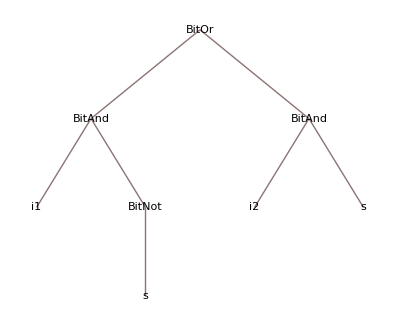

```mathematica
TreeForm[Mux2to1[{s},{i1,i2}]]
```

Mux 4 to 1

```mathematica
PlotCompactInteractiveSystem[{Mux4to1[{s1,s2},{i1,i2,i3,i4}]}]
```

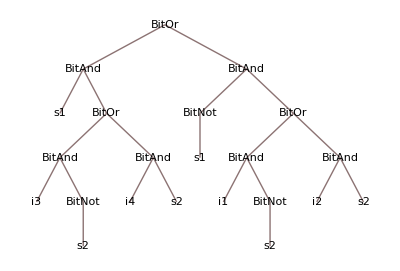

```mathematica
TreeForm[Mux4to1[{s1,s2},{i1,i2,i3,i4}]]
```

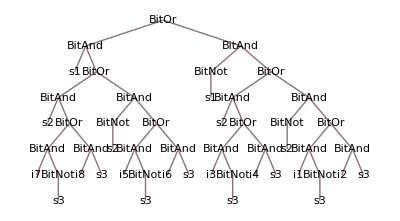

```mathematica
TreeForm[Mux8to1[{s1,s2,s3},{i1,i2,i3,i4,i5,i6,i7,i8}]]
```

```mathematica
PlotCompactInteractiveSystem[{Mux8to1[{s1,s2,s3},{i1,i2,i3,i4,i5,i6,i7,i8}]},ImageSize->700]
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"Animations","Multiplexer8to1","mux.png"}],PlotCompactSystemEvaluations[Mux8to1[{s1,s2,s3},{i1,i2,i3,i4,i5,i6,i7,i8}],ImageSize->700]];
```

$Aborted

### Arbitrary size multiplexer

For an arbitrary sized multiplexer a recursive implementation is used.

```mathematica
MultiplexerNTo1[2,{select_},input__]:=BitOr[BitAnd[First[input],BitNot[select]],BitAnd[Last[input],select]];
MultiplexerNTo1[n_,select_,input__]:=Block[{partInput},
partInput = HalfSplit[input];
MultiplexerNTo1[
2,
{First[select]},
{
MultiplexerNTo1[n/2,Rest[select],First[partInput]],
MultiplexerNTo1[n/2,Rest[select],Last[partInput]]
}
]
];
MultiplexerNToM[n_,m_,select_,input__]:=Table[MultiplexerNTo1[n,select,input[[All,i]]],{i,m}];
```

#### Examples

```mathematica
VisualizeMultiplexer[MultiplexerNTo1[16,#1,#2]&,4]
```

A | B | C | D | Selection
0 | 0 | 0 | 0 | a
0 | 0 | 0 | 1 | b
0 | 0 | 1 | 0 | c
0 | 0 | 1 | 1 | d
0 | 1 | 0 | 0 | e
0 | 1 | 0 | 1 | f
0 | 1 | 1 | 0 | g
0 | 1 | 1 | 1 | h
1 | 0 | 0 | 0 | i
1 | 0 | 0 | 1 | j
1 | 0 | 1 | 0 | k
1 | 0 | 1 | 1 | l
1 | 1 | 0 | 0 | m
1 | 1 | 0 | 1 | n
1 | 1 | 1 | 0 | o
1 | 1 | 1 | 1 | p

```mathematica
selectSymbols = Table[Symbol["s"<>ToString[i]],{i,1,4}];
inputSymbols = Table[Symbol["i"<>ToString[i]],{i,1,16}];
```

```mathematica
MultiplexerNTo1[16,selectSymbols,inputSymbols]
```

BitOr[BitAnd[s1,BitOr[BitAnd[s2,BitOr[BitAnd[s3,BitOr[BitAnd[i15,BitNot[s4]],BitAnd[i16,s4]]],BitAnd[BitNot[s3],BitOr[BitAnd[i13,BitNot[s4]],BitAnd[i14,s4]]]]],BitAnd[BitNot[s2],BitOr[BitAnd[s3,BitOr[BitAnd[i11,BitNot[s4]],BitAnd[i12,s4]]],BitAnd[BitNot[s3],BitOr[BitAnd[i10,s4],BitAnd[i9,BitNot[s4]]]]]]]],BitAnd[BitNot[s1],BitOr[BitAnd[s2,BitOr[BitAnd[s3,BitOr[BitAnd[i7,BitNot[s4]],BitAnd[i8,s4]]],BitAnd[BitNot[s3],BitOr[BitAnd[i5,BitNot[s4]],BitAnd[i6,s4]]]]],BitAnd[BitNot[s2],BitOr[BitAnd[s3,BitOr[BitAnd[i3,BitNot[s4]],BitAnd[i4,s4]]],BitAnd[BitNot[s3],BitOr[BitAnd[i1,BitNot[s4]],BitAnd[i2,s4]]]]]]]]

### Multiplexer selection by opcode

Auxiliary function to pair input-output pairs in a multiplexer by using opcodes.

```mathematica
MuxInputByOpcode1Bit[n_,opcodeAndOutput_]:=Block[{addresses,missing},
addresses = Tuples[{0,1},n]; (* Generate the list of all opcode inputs.  *)
missing = Thread[{Complement[addresses,opcodeAndOutput[[All,1]]],0}]; (* Select the ones with no inputs and map them to zero. *)
Return[SortBy[Join[missing,opcodeAndOutput],First][[All,2]]] (* Join missing opcodes with the given opcodes and sort. *)
];
MuxInputByOpcodeMBit[n_,m_,opcodeAndOutput_]:=Block[{addresses,zero,missing},
addresses = Tuples[{0,1},n]; (* Generate the list of all opcode inputs.  *)
zero = ConstantArray[0,m];
missing = Table[{i,zero},{i,Complement[addresses,opcodeAndOutput[[All,1]]]}]; (* Select the ones with no inputs and map them to zero. *)
Return[SortBy[Join[missing,opcodeAndOutput],First][[All,2]]] (* Join missing opcodes with the given opcodes and sort. *)
];

Mux8ToM[m_,select_,input__]:=Table[Mux8to1[select,input[[All,i]]],{i,m}];

Multiplexer3BitOpcodeTo1Bit[opcode_,opcodeAndOutput_]:=Mux8to1[opcode,MuxInputByOpcode1Bit[3,opcodeAndOutput]];
Multiplexer3BitOpcodeToMBit[m_,opcode_,opcodeAndOutput_]:=Mux8ToM[m,opcode,MuxInputByOpcodeMBit[3,m,opcodeAndOutput]];

Multiplexer8BitOpcodeTo1Bit[opcode_,opcodeAndOutput_]:=MultiplexerNTo1[256,opcode,MuxInputByOpcode1Bit[8,opcodeAndOutput]];
Multiplexer8BitOpcodeToMBit[m_,opcode_,opcodeAndOutput_]:=MultiplexerNToM[256,m,opcode,MuxInputByOpcodeMBit[8,m,opcodeAndOutput]];
```

#### Example

```mathematica
MuxInputByOpcodeMBit[3,8,
{
{ALUOpCode["Add"],{a1,a2,a3,a4,a5,a6,a7,a8}},
{ALUOpCode["Substract"],{s1,s2,s3,s4,s5,s6,s7,s8}},
{ALUOpCode["Decrement"],{d1,d2,d3,d4,d5,d6,d7,d8}},
{ALUOpCode["Increment"],{i1,i2,i3,i4,i5,i6,i7,i8}},
{ALUOpCode["Pass"],{p1,p2,p3,p4,p5,p6,p7,p8}}
}
]
```

{{a1,a2,a3,a4,a5,a6,a7,a8},{s1,s2,s3,s4,s5,s6,s7,s8},{i1,i2,i3,i4,i5,i6,i7,i8},{d1,d2,d3,d4,d5,d6,d7,d8},{p1,p2,p3,p4,p5,p6,p7,p8},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

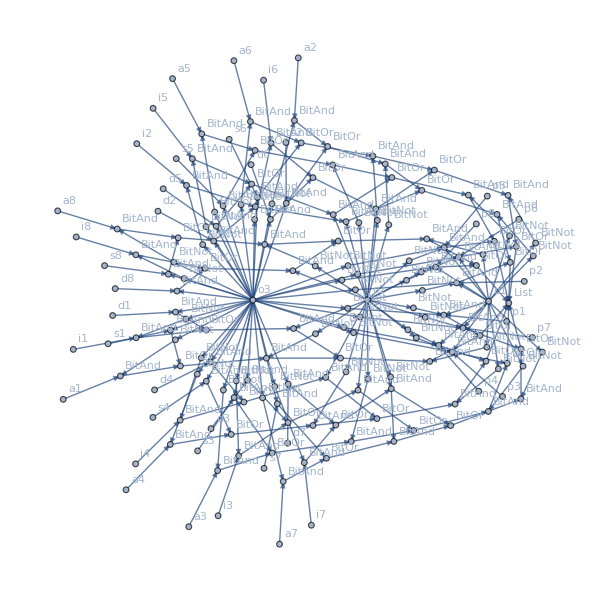

```mathematica
CompactTreeForm[
Multiplexer3BitOpcodeToMBit[8,{o1,o2,o3},
{
{ALUOpCode["Add"],{a1,a2,a3,a4,a5,a6,a7,a8}},
{ALUOpCode["Substract"],{s1,s2,s3,s4,s5,s6,s7,s8}},
{ALUOpCode["Increment"],{i1,i2,i3,i4,i5,i6,i7,i8}},
{ALUOpCode["Decrement"],{d1,d2,d3,d4,d5,d6,d7,d8}},
{ALUOpCode["Pass"],{p1,p2,p3,p4,p5,p6,p7,p8}}
}
],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->600,
VertexSize->0.6,
"ShowLabels"->Automatic
]
```

```mathematica
Multiplexer3BitOpcodeToMBit[8,ALUOpCode["Add"],
{
{ALUOpCode["Add"],{a1,a2,a3,a4,a5,a6,a7,a8}},
{ALUOpCode["Substract"],{s1,s2,s3,s4,s5,s6,s7,s8}},
{ALUOpCode["Increment"],{i1,i2,i3,i4,i5,i6,i7,i8}},
{ALUOpCode["Decrement"],{d1,d2,d3,d4,d5,d6,d7,d8}},
{ALUOpCode["Pass"],{p1,p2,p3,p4,p5,p6,p7,p8}}
}
]
```

{a1,a2,a3,a4,a5,a6,a7,a8}

## ALU

La ALU (Arithmetic Logical Unit) es el circuito del procesador que se encarga de realizar operaciones aritméticas. La ALU requiere dos dígitos A y B y un Opcode que indica la operación a realizar.
Es posible acceder al Opcode por medio de un alias, como por ejemplo:

```mathematica
ALUOpCode["Add"]
```

{0,0,0}

```mathematica
ALUOpCode["Substract"]
```

{0,0,1}

La lista de todos los Opcodes disponibles en la ALU es:

```mathematica
aluOpcodes
```

{Add→{0,0,0},Substract→{0,0,1},Increment→{0,1,0},Decrement→{0,1,1},Pass→{1,0,0}}

Al realizar cada operación la ALU devuelve además del resultado, un código de status que indica las propiedades de la operación realizada.

### Half adder

El Half Adder, Full Adder, y Ripple Carry Adder son circuitos para implementar sumas

-Graphics-

```mathematica
HalfAdder[a_,b_]:={BitAnd[a,b],BitXor[a,b]};
```

#### Ejemplo

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

#### Visualización

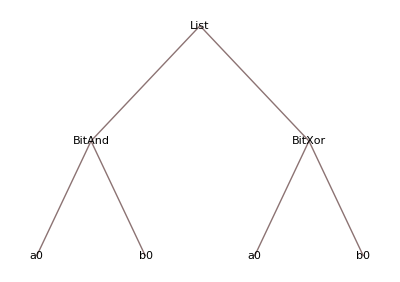

```mathematica
TreeForm[HalfAdder[a0,b0]]
```

```mathematica
HalfAdder[a0,b0]
```

{BitAnd[a0,b0],BitXor[a0,b0]}

```mathematica
PlotCompactInteractiveSystem[HalfAdder[a0,b0],ImageSize->Small]
```

### Full adder

-Graphics-

```mathematica
FullAdder[a_,b_,c_]:=Block[{halfAdd1,halfAdd2},
halfAdd1 = HalfAdder[a,b];
halfAdd2 = HalfAdder[Last[halfAdd1],c];
{BitOr[First[halfAdd1],First[halfAdd2]],Last[halfAdd2]}
];
```

#### Ejemplo

```mathematica
VisualizeAdder[FullAdder,3,"Carry"]
```

A | B | C | Carry | Result
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1

#### Visualización

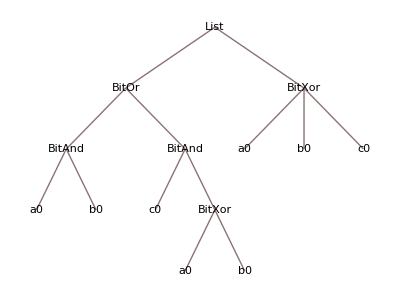

```mathematica
TreeForm[FullAdder[a0,b0,c0]]
```

```mathematica
PlotCompactInteractiveSystem[FullAdder[a0,b0,c0],ImageSize->Small]
```

### Ripple carry adder

-Graphics-

```mathematica
ALUAdder[A_,B_,carry_:0]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[B];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{carry,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{First[bigEndianSum],Rest[bigEndianSum]}];
];
```

#### Ejemplo

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUAdder,Transpose[pairs]];
labels = {"A","B","Carry","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

A | B | Carry | Result
{0,0} | {0,0} | 0 | {0,0}
{0,0} | {0,1} | 0 | {0,1}
{0,0} | {1,0} | 0 | {1,0}
{0,0} | {1,1} | 0 | {1,1}
{0,1} | {0,0} | 0 | {0,1}
{0,1} | {0,1} | 0 | {1,0}
{0,1} | {1,0} | 0 | {1,1}
{0,1} | {1,1} | 1 | {0,0}
{1,0} | {0,0} | 0 | {1,0}
{1,0} | {0,1} | 0 | {1,1}
{1,0} | {1,0} | 1 | {0,0}
{1,0} | {1,1} | 1 | {0,1}
{1,1} | {0,0} | 0 | {1,1}
{1,1} | {0,1} | 1 | {0,0}
{1,1} | {1,0} | 1 | {0,1}
{1,1} | {1,1} | 1 | {1,0}

#### Visualización

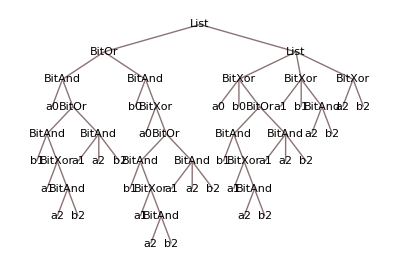

```mathematica
TreeForm[ALUAdder[{a0,a1,a2},{b0,b1,b2}]]
```

En esencia no deja de ser una composición de operaciones binarias

```mathematica
ALUAdder[{a0,a1,a2},{b0,b1,b2}]
```

{BitOr[BitAnd[a0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]],BitAnd[b0,BitXor[a0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]]]],{BitXor[a0,b0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]],BitXor[a1,b1,BitAnd[a2,b2]],BitXor[a2,b2]}}

```mathematica
PlotCompactInteractiveSystem[ALUAdder[{a1,a2,a3},{b1,b2,b3}],EdgeStyle->Thick]
```

### Substractor

```mathematica
ALUSubstractor[A_,B_,borrow_:1]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[BitNot[B]];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{borrow,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{BitNot[First[bigEndianSum]],Rest[bigEndianSum]}];
];
```

#### Ejemplo

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUSubstractor,Transpose[pairs]];
labels = {"A","B","Borrow","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

#### Visualización

```mathematica
TreeForm[ALUSubstractor[{a0,a1,a2},{b0,b1,b2}]]
```

### Opcodes

The control unit selects which operation result to get by sending an opcode to the ALU.

```mathematica
aluMnemonics = {"Add","Substract","Increment","Decrement","Pass"};
aluOpcodes = Thread[aluMnemonics->Take[Tuples[{0,1},3],Length[aluMnemonics]]];
revAluOpcodes = Map[Reverse,aluOpcodes];
ALUOpCode[mnemonic_]:=ReplaceAll[mnemonic,aluOpcodes];
```

```mathematica
Column@aluOpcodes
```

Add→{0,0,0}
Substract→{0,0,1}
Increment→{0,1,0}
Decrement→{0,1,1}
Pass→{1,0,0}

### Execution

Flags

```mathematica
ALUZero[a_]:=BitNot[Apply[BitOr,a]];
ALUNotZero[a_]:=Apply[BitOr,a];
ALUParity[a_]:=Apply[BitXor,a];
```

ALU interface

```mathematica
ALUExecute[opcode_,a_,b_]:=Block[
{
add,substract,
increment,decrement,pass,output,positiveFlag,
negativeFlag,parityFlag
},

add = ALUAdder[a,b];
substract = ALUSubstractor[a,b];
increment = ALUAdder[PadLeft[{1},Length[a]],a];
decrement = ALUSubstractor[a,PadLeft[{1},Length[a]]];
pass = a;

output = Multiplexer3BitOpcodeToMBit[Length[a],opcode,
{
{ALUOpCode["Add"],Last[add]},
{ALUOpCode["Substract"],Last[substract]},
{ALUOpCode["Increment"],Last[increment]},
{ALUOpCode["Decrement"],Last[decrement]},
{ALUOpCode["Pass"],pass}
}
];

positiveFlag = Multiplexer3BitOpcodeTo1Bit[opcode,
{
{ALUOpCode["Add"],1},
{ALUOpCode["Substract"],BitNot[First[substract]]},
{ALUOpCode["Increment"],1},
{ALUOpCode["Decrement"],BitNot[First[decrement]]},
{ALUOpCode["Pass"],0}
}
];

negativeFlag = Multiplexer3BitOpcodeTo1Bit[opcode,
{
{ALUOpCode["Add"],0},
{ALUOpCode["Substract"],First[substract]},
{ALUOpCode["Increment"],0},
{ALUOpCode["Decrement"],First[decrement]},
{ALUOpCode["Pass"],0}
}
];

Return[<|"Positive"->positiveFlag,"Negative"->negativeFlag,"Zero"->ALUZero[output],"NotZero"->ALUNotZero[output],"Parity"->ALUParity[output],"Result"->output|>];
];
ALUExecute[opcode_,a_]:=ALUExecute[opcode,a,ConstantArray[0,Length[a]]];

ALUClear[]:=Block[{},
WriteFlag[0,"ALUFlagPositive"];
WriteFlag[0,"ALUFlagNegative"];
WriteFlag[0,"ALUFlagZero"];
WriteFlag[0,"ALUFlagNotZero"];
WriteFlag[0,"ALUFlagParity"];
];
```

#### Visualization

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Add"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

18

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Substract"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

4

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Increment"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

12

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Decrement"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

10

```mathematica
ALUExecute[ALUOpCode["Pass"],DecimalToBinary[11],DecimalToBinary[7]]
```

<|Positive→0,Negative→0,Zero→0,NotZero→1,Parity→1,Result→{0,0,0,0,1,0,1,1}|>

```mathematica
PlotCompactInteractiveSystem[
Values[ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}]],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->800,
VertexSize->0.6,
"ShowLabels"->None
]
```

```mathematica
ListAnimate[
PlotCompactSystemEvaluations[
Values[ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}]],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->800,
VertexSize->0.6,
"ShowLabels"->None
]
]
```

## Memory

### And-Or Latch

In electronics, a flip-flop or latch is a circuit that has two stable states and can be used to store state information. A flip-flop is a bistable multivibrator. The circuit can be made to change state by signals applied to one or more control inputs and will have one or two outputs. It is the basic storage element in sequential logic. Flip-flops and latches are fundamental building blocks of digital electronics systems used in computers, communications, and many other types of systems.

-Graphics-

```mathematica
AndOrLatch[set_,reset_,tag_]:=MemoryEvaluate[BitAnd[BitOr[#,set],BitNot[reset]]&,tag];
```

It is the base circuit for all the following memory cells below.

#### Visualization

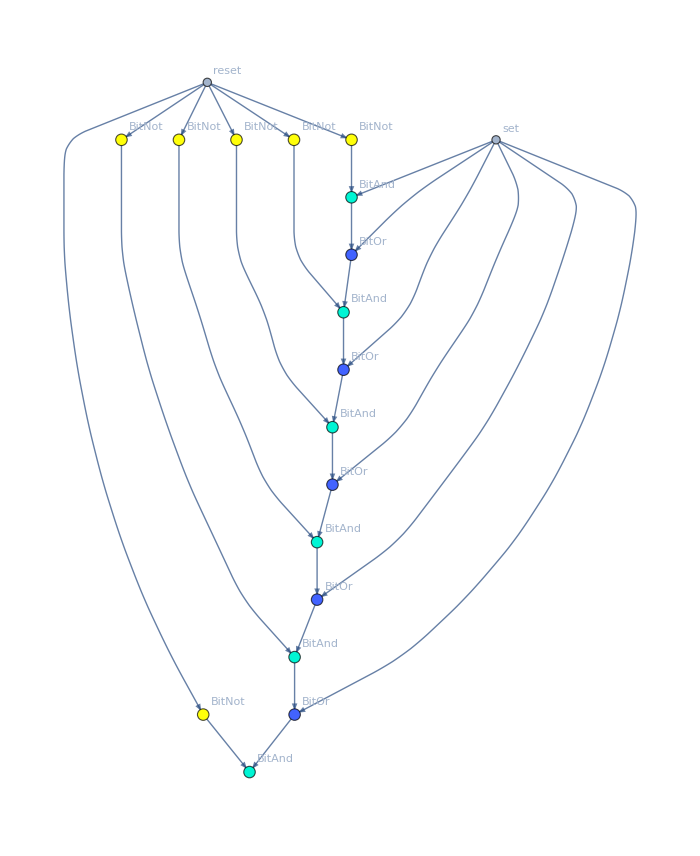

```mathematica
Last[Table[CompactHighlightedTreeForm[AndOrLatch[set,reset,tag0],ImageSize->700],6]]
```

### Gated Latch

-Graphics-

Image source: Crash Course Computer Science

```mathematica
GatedLatch[dataInput_,writeEnable_,tag_]:=AndOrLatch[BitAnd[dataInput,writeEnable],BitAnd[BitNot[dataInput],writeEnable],tag];
```

This circuit is useful to store 1 bit flags.

```mathematica
Flag[dataInput_,writeEnable_,tag_]:=GatedLatch[dataInput,writeEnable,tag];
ReadFlag[tag_]:=GatedLatch[0,0,tag];
WriteFlag[dataInput_,tag_]:=GatedLatch[dataInput,1,tag];
```

#### Visualization

```mathematica
Table[TreeForm[GatedLatch[dataInput,writeEnable,tag3],ImageSize->Medium],3]
```

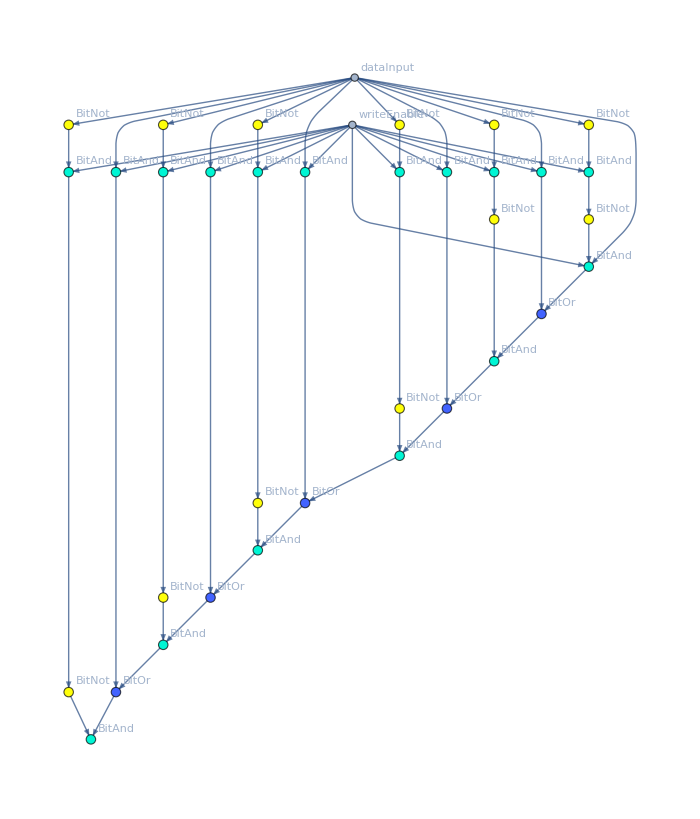

```mathematica
Last[Table[CompactHighlightedTreeForm[GatedLatch[dataInput,writeEnable,tag3],ImageSize->700],6]]
```

### 8 bit memory cell

Source: Crash Course Computer Science

```mathematica
MultiplexerNTo1[256,address,input__]
```

```mathematica
BitwiseSame[n1_,n2_]:=Apply[BitAnd,Map[BitNot[Apply[BitXor,#]]&,Thread[{n1,n2}]]];
Bit8AddressCell[dataInput_,writeEnable_,address__,tag_]:=MultiplexerNTo1[
256,
address,
Table[GatedLatch[dataInput,BitAnd[writeEnable,BitwiseSame[IntegerDigits[i-1,2,8],address]],StringJoin[tag,"bit_",ToString[i]]],{i,1,256}]
];
```

```mathematica
Bit8AddressCell[0,1,{0,0,0,0,0,0,0,0},"mdsld"]
```

0

```mathematica
CompactHighlightedTreeForm[
Bit8AddressCell[b,wr,{a1,a2,a3,a4,a5,a6,a7,a8},"idk"],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.005}],
ImageSize->1500,
VertexSize->0.6,
"ShowLabels"->None
]
```

### 8 bit address block

Source: Crash Course Computer Science

```mathematica
Bit8AddressBlock[dataInput__/;Length[dataInput]==8,writeEnable_,address__,tag_]:=Table[Bit8AddressCell[Part[dataInput,i],writeEnable,address,StringJoin[tag,"bit_",ToString[i]]],{i,8}];

ReadBit8AddressBlock[address__,tag_]:=Bit8AddressBlock[{0,0,0,0,0,0,0,0},0,address,tag];
WriteBit8AddressBlock[dataInput__/;Length[dataInput]==8,address__,tag_]:=Bit8AddressBlock[dataInput,1,address,tag];

ResetBit8AddressBlock[tag_,size_]:=Block[{addresses},
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,size]];
Map[WriteBit8AddressBlock[{0,0,0,0,0,0,0,0},#1,tag]&,addresses];
];
```

#### Visualization

```mathematica
TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},wr1,{a1,a2,a3,a4,a5,a6,a7,a8},"exampletag3"],VertexLabeling->Automatic,ImageSize->1500]
```

Recursive visualization

```mathematica
trees = Table[TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4,a5,a6,a7,a8},"manip"],VertexLabeling->Automatic,ImageSize->1300],15];
Manipulate[trees[[i]],{i,1,Length[trees],1},SaveDefinitions->True]
```

```mathematica
Table[CompactExprMatrixPlot[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},wr1,{a1,a2,a3,a4,a5,a6,a7,a8},"exampletag5"]],3]
```

## Registers

Registers are fixed sized memory blocks that are used to store special digits, like memory position, data from which operations can be performed and so on.
Since this is a 8-bit machine, 8-bit registers are used as general purpose registers and memory address registers.
3-bit registers are used by the control unit to store ALU opcodes.

Source: Crash Course Computer Science

### 3 and 8 bit registers

```mathematica
Bit3Register[dataInput__,writeEnable_,tag_]:=Table[
GatedLatch[
Part[dataInput,index],
writeEnable,
StringJoin[tag,"_bit3register",ToString[index]]
],
{index,1,3}
];
ReadBit3Register[tag_]:=Bit3Register[{0,0,0},0,tag];
WriteBit3Register[dataInput__,tag_]:=Bit3Register[dataInput,1,tag];

Bit8Register[dataInput__,writeEnable_,tag_]:=Table[
GatedLatch[
Part[dataInput,index],
writeEnable,
StringJoin[tag,"_bit8register",ToString[index]]
],
{index,1,8}
];
ReadBit8Register[tag_]:=Bit8Register[{0,0,0,0,0,0,0,0},0,tag];
WriteBit8Register[dataInput__,tag_]:=Bit8Register[dataInput,1,tag];
```

#### Examples:

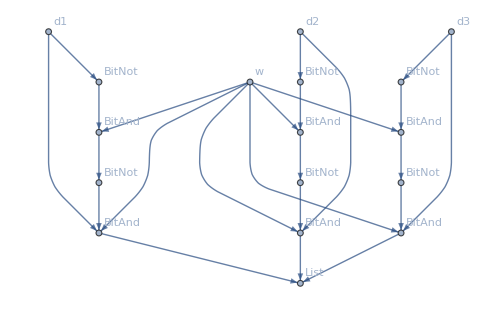
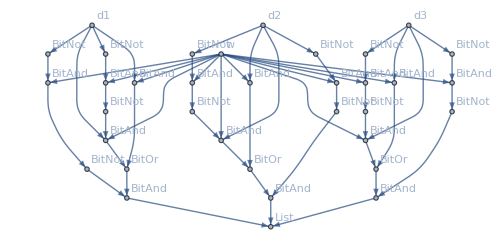
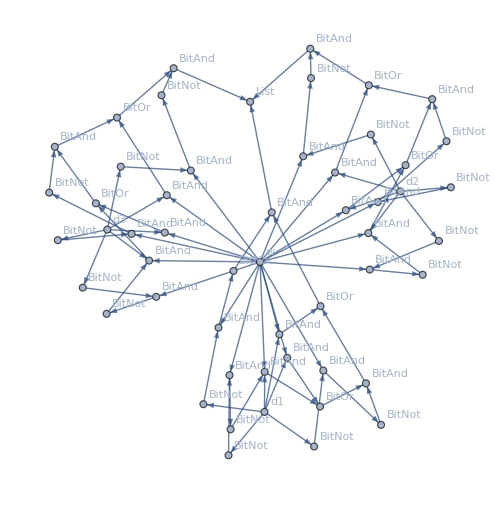
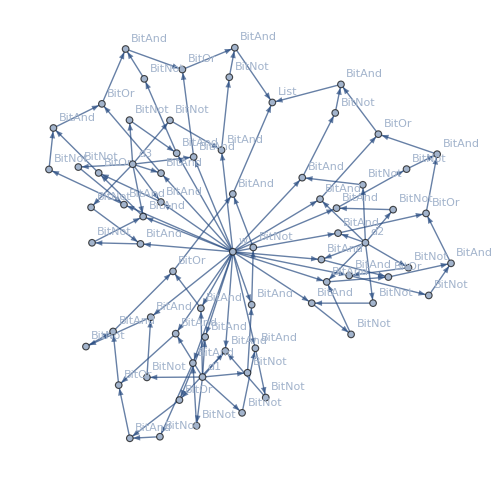
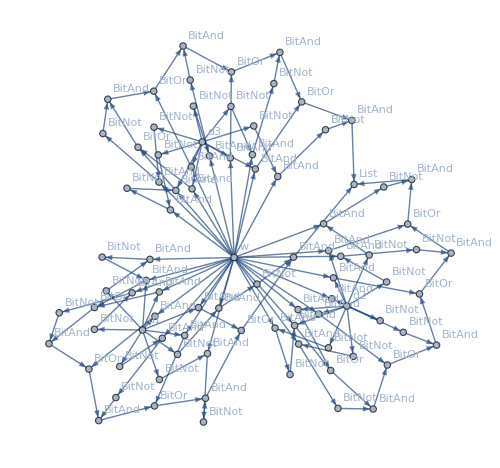
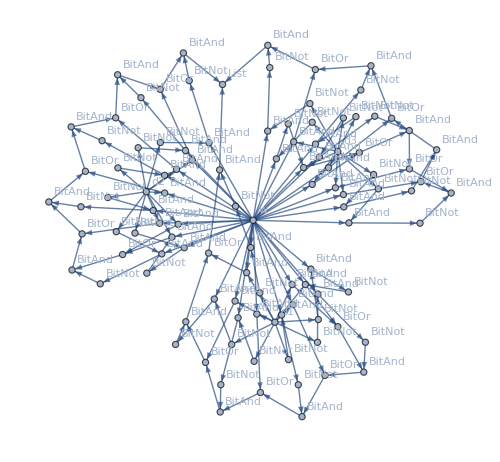

```mathematica
Table[CompactTreeForm[Bit3Register[{d1,d2,d3},w,"idk233"],ImageSize->500],6]
```

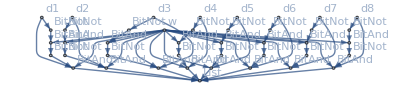
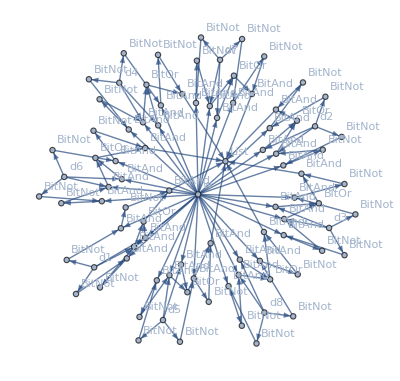
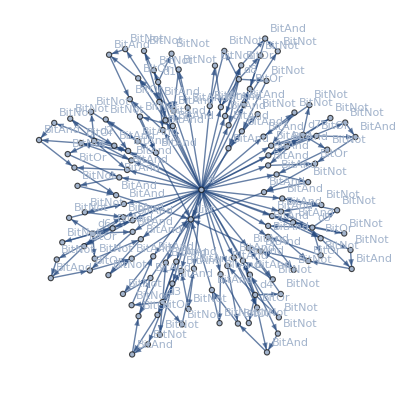
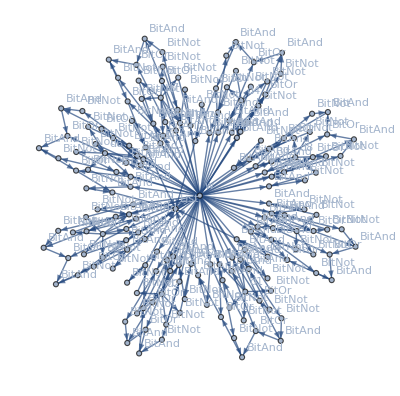
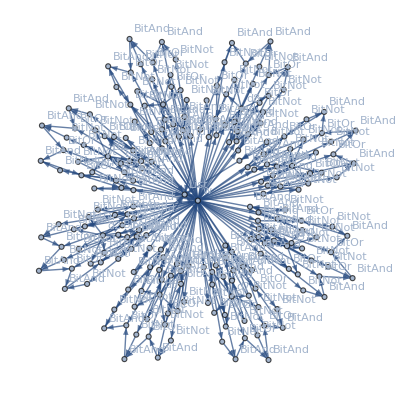
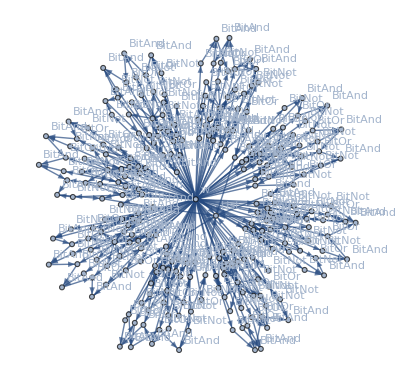

```mathematica
Table[CompactTreeForm[Bit8Register[{d1,d2,d3,d4,d5,d6,d7,d8},w,"idk11"],ImageSize->400],6]
```

## CPU

This CPU contains two general purpose registers A and B which can hold 8 bit values, an addressRegister which points to the current execution address, a instructionRegister and a parameterRegister also of length 8 bit and a stackPointerRegister that cannot exceed in value the maximum stack depth of 8.

The arithmetic and logical unit has the following flags
ALUPositiveFlag
ALUNegativeFlag
ALUZeroFlag
ALUNotZeroFlag
ALUParityFlag

Here is a description of the instruction set:

LoadA address, loads the content of RAM at address to the A register.
LoadB address, loads the content of RAM at address to the B register.
SetA value, sets register A with value.
SetB value, sets register B with value.
Store address, stores the value of register A to the memory location address.
Add, adds the value of register A to the value of register B and store it in register A.
Substract, substracts the value of register A to the value of register B and store it in register A.
Increment, increments by one unit the value of register A.
Decrement, decrement by one unit the value of register A.
Jump address, sets addressRegister to the value of address.
JumpPos address, sets addressRegister to the value of address if the register ALUFlagPositive has value of 1.
JumpNeg address, sets addressRegister to the value of address if the register ALUFlagNegative has value of 1.
JumpZero address, sets addressRegister to the value of address if the register ALUFlagZero has value of 1.
JumpNotZero address, sets addressRegister to the value of address if the register ALUFlagNotZero has value of 1.
JumpOdd address, sets addressRegister to the value of address if the register ALUFlagParity has value of 1.
Call address, stores current addressRegister value on the stack and  jump to address.
Return, sets addressRegister to the last value of the stack. If the stack is empty, halt the machine.
Print address, prints the value of RAM at address in the output buffer.
Halt stops the computation.

### Control unit initialization

CUClear[] starts the control unit and can also be used to reset the machine.

```mathematica
CUClear[]:=Block[{},
ResetBit8AddressBlock["Stack",8];
WriteBit8Register[{0,0,0,0,0,0,0,0},"InstructionAddressRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,1},"ParameterAddressRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"InstructionRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"ParameterRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"StackPointerRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"RegisterA"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"RegisterB"];
WriteFlag[0,"Ram Read-Enable"];
WriteFlag[0,"Ram Write-Enable"];
WriteFlag[0,"Stack Read-Enable"];
WriteFlag[0,"Stack Write-Enable"];
WriteFlag[0,"RegisterA Read-Enable"];
WriteFlag[0,"RegisterB Read-Enable"];
WriteFlag[0,"RegisterA Write-Enable"];
WriteFlag[0,"RegisterB Write-Enable"];
WriteFlag[0,"ALU Instruction"];
WriteFlag[0,"ALU Opcode"];
WriteFlag[0,"Print Enable"];
WriteFlag[0,"Halt"];
outputBuffer = {};
];
CUClear[];
```

### Opcodes

```mathematica
cpuMnemonics = {
"LoadA","LoadB","SetA","SetB","Store","Add",
"Substract","Increment","Decrement","Jump","JumpPos","JumpNeg","JumpZero","JumpNotZero","JumpOdd",
"Call","Return","Print","Halt"
};
opcodes = Thread[cpuMnemonics->Take[Tuples[{0,1},8],Length[cpuMnemonics]]];
revOpcodes = Map[Reverse,opcodes];
OpCode[mnemonic_]:=ReplaceAll[mnemonic,opcodes];
```

```mathematica
Column[opcodes]
```

LoadA→{0,0,0,0,0,0,0,0}
LoadB→{0,0,0,0,0,0,0,1}
SetA→{0,0,0,0,0,0,1,0}
SetB→{0,0,0,0,0,0,1,1}
Store→{0,0,0,0,0,1,0,0}
Add→{0,0,0,0,0,1,0,1}
Substract→{0,0,0,0,0,1,1,0}
Increment→{0,0,0,0,0,1,1,1}
Decrement→{0,0,0,0,1,0,0,0}
Jump→{0,0,0,0,1,0,0,1}
JumpPos→{0,0,0,0,1,0,1,0}
JumpNeg→{0,0,0,0,1,0,1,1}
JumpZero→{0,0,0,0,1,1,0,0}
JumpNotZero→{0,0,0,0,1,1,0,1}
JumpOdd→{0,0,0,0,1,1,1,0}
Call→{0,0,0,0,1,1,1,1}
Return→{0,0,0,1,0,0,0,0}
Print→{0,0,0,1,0,0,0,1}
Halt→{0,0,0,1,0,0,1,0}

### Fetch

Reads InstructionAddressRegister, ParameterAddressRegister, and writes InstructionRegister, ParameterRegister.

```mathematica
CUFetch[]:=Block[{instructionAddress,parameterAddress,instruction,parameter},
instructionAddress = ReadBit8Register["InstructionAddressRegister"];
parameterAddress = Last[ALUAdder[instructionAddress,{0,0,0,0,0,0,0,1}]];
instruction = ReadBit8AddressBlock[instructionAddress,"RAM"];
parameter = ReadBit8AddressBlock[parameterAddress,"RAM"];
WriteBit8Register[instruction,"InstructionRegister"];
WriteBit8Register[parameter,"ParameterRegister"];

Return[<|"Instruction Address"->instructionAddress,"Parameter Address"->parameterAddress, "Instruction Register"->instruction, "Parameter Register"->parameter,"Instruction opcode"->ReplaceAll[instruction,revOpcodes]|>];
];
```

```mathematica
CUFetch[]
```

<|Instruction Address→{0,0,0,0,0,0,0,0},Parameter Address→{0,0,0,0,0,0,0,1},Instruction Register→{0,0,0,0,0,0,0,0},Parameter Register→{0,0,0,0,0,0,0,0},Instruction opcode→LoadA|>

### Decode

Reads the InstructionRegister, and writes the following flags:
Ram Read-Enable
Ram Write-Enable
Stack Read-Enable
Stack Write-Enable
RegisterA Read-Enable
RegisterA Write-Enable
RegisterB Write-Enable
Jump, JumpPos, JumpNeg, JumpZero, JumpNotZero
ALU Instruction
ALU Opcode
Print Enable

This flags are used to direct the output result to the adequate registers or memory cells.

```mathematica
CUDecode[]:=Block[
{
opcode,halt,ramReadEnable,ramWriteEnable,stackReadEnable,stackWriteEnable,registerAReadEnable,registerAWriteEnable,
registerBWriteEnable,aluOpcode,aluInstruction, jumpEnable,jumpPosEnable, jumpNegEnable,
jumpZeroEnable,jumpNotZeroEnable,printEnable,setFromParam
},

opcode = ReadBit8Register["InstructionRegister"];

halt = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Halt"],1}
}
];
WriteFlag[halt,"Halt"];

ramReadEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["LoadA"],1},
{OpCode["LoadB"],1}
}
];
WriteFlag[ramReadEnable,"Ram Read-Enable"];

ramWriteEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Store"],1}
}
];
WriteFlag[ramWriteEnable,"Ram Write-Enable"];

stackReadEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Return"],1}
}
];
WriteFlag[stackReadEnable,"Stack Read-Enable"];

stackWriteEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Call"],1}
}
];
WriteFlag[stackWriteEnable,"Stack Write-Enable"];

registerAReadEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Store"],1},
{OpCode["Print"],1}
}
];
WriteFlag[registerAReadEnable,"RegisterA Read-Enable"];

registerAWriteEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["LoadA"],1},
{OpCode["SetA"],1},
{OpCode["Add"],1},
{OpCode["Substract"],1},
{OpCode["Increment"],1},
{OpCode["Decrement"],1}
}
];
WriteFlag[registerAWriteEnable,"RegisterA Write-Enable"];

registerBWriteEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["LoadB"],1},
{OpCode["SetB"],1}
}
];
WriteFlag[registerBWriteEnable,"RegisterB Write-Enable"];

jumpEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Jump"],1}
}
];
WriteFlag[jumpEnable,"Jump"];

jumpPosEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["JumpPos"],1}
}
];
WriteFlag[jumpPosEnable,"JumpPos"];

jumpNegEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["JumpNeg"],1}
}
];
WriteFlag[jumpNegEnable,"JumpNeg"];

jumpZeroEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["JumpZero"],1}
}
];
WriteFlag[jumpZeroEnable,"JumpZero"];

jumpNotZeroEnable = Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["JumpNotZero"],1}
}
];
WriteFlag[jumpNotZeroEnable,"JumpNotZero"];

aluInstruction =  Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Add"],1},
{OpCode["Substract"],1},
{OpCode["Increment"],1},
{OpCode["Decrement"],1}
}
];
WriteFlag[aluInstruction,"ALU Instruction"];

aluOpcode =  Multiplexer8BitOpcodeToMBit[3,opcode,
{
{OpCode["Add"],ALUOpCode["Add"]},
{OpCode["Substract"],ALUOpCode["Substract"]},
{OpCode["Increment"],ALUOpCode["Increment"]},
{OpCode["Decrement"],ALUOpCode["Decrement"]}
}
];
WriteBit3Register[aluOpcode,"ALU Opcode"];

printEnable =  Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["Print"],1}
}
];
WriteFlag[printEnable,"Print Enable"];

setFromParam =  Multiplexer8BitOpcodeTo1Bit[opcode,
{
{OpCode["SetA"],1},
{OpCode["SetB"],1}
}
];
WriteFlag[setFromParam,"Set From Parameter"];

Return[
<|
"Ram Read-Enable"->ramReadEnable,"Ram Write-Enable"->ramWriteEnable,
"Stack Read-Enable"->stackReadEnable,"Stack Write-Enable"->stackWriteEnable,
"RegisterA Read-Enable"->registerAReadEnable,"RegisterA Write-Enable"->registerAWriteEnable,"RegisterB Write-Enable"->registerBWriteEnable,
"Jump"->jumpEnable,"JumpPos"->jumpPosEnable,"JumpNeg"->jumpNegEnable,"JumpZero"->jumpZeroEnable,"JumpNotZero"->jumpNotZeroEnable,
"ALU Instruction"->aluInstruction,"ALU Opcode"->aluOpcode,
"Print Enable"->printEnable,"Set From Parameter"->setFromParam
|>
];
];
```

#### Visualization

```mathematica
CUClear[];
```

```mathematica
op1 = WriteBit8Register[{a1,a2,a3,a4,a5,a6,a7,a8},"InstructionRegister"];
op2 = CUDecode[];
```

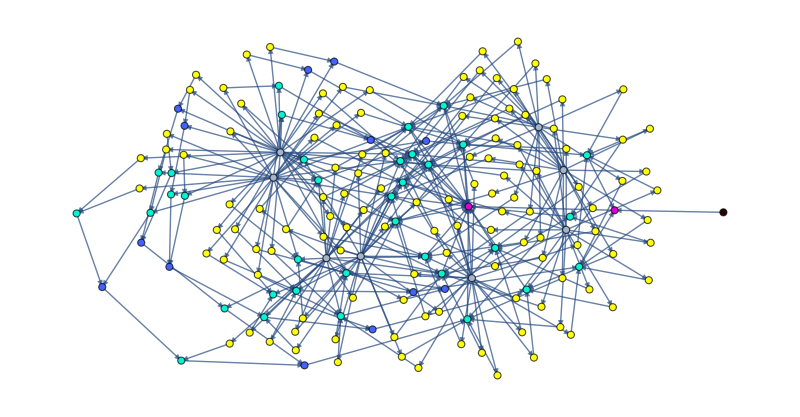

```mathematica
CompactHighlightedTreeForm[
Values[op2],
"ShowLabels"->False,
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->800,
VertexSize->0.6
]
```

### Execute

```mathematica
CUExecute[]:=Block[{param,readFromRam,aluResult,nextInstructionAddress,nextStackPointer,stackLast,stackLastAddress,status = "Running"},
param = ReadBit8Register["ParameterRegister"];
readFromRam = ReadBit8AddressBlock[param,"RAM"];

(* Print *)
If[ReadFlag["Print Enable"]==1, AppendTo[outputBuffer,BinaryToDecimal[readFromRam]]];

(* Set operations *)
Bit8Register[param,BitAnd[ReadFlag["RegisterA Write-Enable"],ReadFlag["Set From Parameter"],BitNot[ReadFlag["ALU Instruction"]]],"RegisterA"];
Bit8Register[param,BitAnd[ReadFlag["RegisterB Write-Enable"],ReadFlag["Set From Parameter"],BitNot[ReadFlag["ALU Instruction"]]],"RegisterB"];

(* Load operations *)
Bit8Register[readFromRam,BitAnd[ReadFlag["RegisterA Write-Enable"],BitNot[ReadFlag["Set From Parameter"]],BitNot[ReadFlag["ALU Instruction"]]],"RegisterA"];
Bit8Register[readFromRam,BitAnd[ReadFlag["RegisterB Write-Enable"],BitNot[ReadFlag["Set From Parameter"]],BitNot[ReadFlag["ALU Instruction"]]],"RegisterB"];

(* ALU operations *)
aluResult = ALUExecute[ReadBit3Register["ALU Opcode"],ReadBit8Register["RegisterA"],ReadBit8Register["RegisterB"]];
Bit8Register[aluResult["Result"],BitAnd[ReadFlag["RegisterA Write-Enable"],ReadFlag["ALU Instruction"]],"RegisterA"];
Flag[aluResult["Positive"],ReadFlag["ALU Instruction"],"ALUFlagPositive"];
Flag[aluResult["Negative"],ReadFlag["ALU Instruction"],"ALUFlagNegative"];
Flag[aluResult["Zero"],ReadFlag["ALU Instruction"],"ALUFlagZero"];
Flag[aluResult["NotZero"],ReadFlag["ALU Instruction"],"ALUFlagNotZero"];
Flag[aluResult["Parity"],ReadFlag["ALU Instruction"],"ALUFlagParity"];

(* Store operations *)
Bit8AddressBlock[ReadBit8Register["RegisterA"],ReadFlag["Ram Write-Enable"],param,"RAM"];

(* Instruction address operations *)
Bit8Register[param,
BitOr[
ReadFlag["Jump"],
BitAnd[ReadFlag["JumpPos"],ReadFlag["ALUFlagPositive"]],
BitAnd[ReadFlag["JumpNeg"],ReadFlag["ALUFlagNegative"]],
BitAnd[ReadFlag["JumpZero"],ReadFlag["ALUFlagZero"]],
BitAnd[ReadFlag["JumpNotZero"],ReadFlag["ALUFlagNotZero"]],
BitAnd[ReadFlag["JumpOdd"],ReadFlag["ALUFlagParity"]]
],
"InstructionAddressRegister"
];

nextInstructionAddress = Last[ALUAdder[ReadBit8Register["InstructionAddressRegister"],{0,0,0,0,0,0,1,0}]];
Bit8Register[nextInstructionAddress,
BitOr[
BitAnd[
BitNot[ReadFlag["Jump"]],
BitNot[ReadFlag["JumpPos"]],
BitNot[ReadFlag["JumpNeg"]],
BitNot[ReadFlag["JumpZero"]],
BitNot[ReadFlag["JumpNotZero"]],
BitNot[ReadFlag["JumpOdd"]]
],
BitAnd[ReadFlag["JumpPos"],BitNot[ReadFlag["ALUFlagPositive"]]],
BitAnd[ReadFlag["JumpNeg"],BitNot[ReadFlag["ALUFlagNegative"]]],
BitAnd[ReadFlag["JumpZero"],BitNot[ReadFlag["ALUFlagZero"]]],
BitAnd[ReadFlag["JumpNotZero"],BitNot[ReadFlag["ALUFlagNotZero"]]],
BitAnd[ReadFlag["JumpOdd"],BitNot[ReadFlag["ALUFlagParity"]]]
],
"InstructionAddressRegister"
];

(* Call operations on stack *)
Bit8AddressBlock[nextInstructionAddress,ReadFlag["Stack Write-Enable"],ReadBit8Register["StackPointerRegister"],"Stack"];
nextStackPointer = Last[ALUAdder[ReadBit8Register["StackPointerRegister"],{0,0,0,0,0,0,0,1}]];
Bit8Register[nextStackPointer,ReadFlag["Stack Write-Enable"],"StackPointerRegister"];
If[BinaryToDecimal[ReadBit8Register["StackPointerRegister"]]>7,
status = "Stack overflow";
WriteFlag[1,"Halt"];
];
Bit8Register[param,ReadFlag["Stack Write-Enable"],"InstructionAddressRegister"];

(* Return operations on stack *)
stackLastAddress = Last[ALUSubstractor[ReadBit8Register["StackPointerRegister"],{0,0,0,0,0,0,0,1}]];
stackLast = ReadBit8AddressBlock[stackLastAddress,"Stack"];
Bit8Register[stackLast,ReadFlag["Stack Read-Enable"],"InstructionAddressRegister"];
Bit8AddressBlock[{0,0,0,0,0,0,0,0},ReadFlag["Stack Read-Enable"],stackLastAddress,"Stack"];
nextStackPointer = ALUSubstractor[ReadBit8Register["StackPointerRegister"],{0,0,0,0,0,0,0,1}];
Bit8Register[Last[nextStackPointer],BitAnd[BitNot[First[nextStackPointer]],ReadFlag["Stack Read-Enable"]],"StackPointerRegister"];
If[First[nextStackPointer] == 1 && ReadFlag["Stack Read-Enable"],
status = "Halted";
WriteFlag[1,"Halt"];
];

<|
"RegisterA"-> ReadBit8Register["RegisterA"],"RegisterB"->ReadBit8Register["RegisterB"],
"InstructionAddressRegister"->ReadBit8Register["InstructionAddressRegister"],"Status"->status
|>

];
```

#### Example

Load the value 00000011 to register A.

```mathematica
CUClear[];
```

```mathematica
WriteBit8Register[OpCode["SetA"],"InstructionRegister"];
CUDecode[];
WriteBit8Register[{0,0,0,0,0,0,1,1},"ParameterRegister"];
```

```mathematica
op = CUExecute[]
```

<|RegisterA→{0,0,0,0,0,0,1,1},RegisterB→{0,0,0,0,0,0,0,0},InstructionAddressRegister→{0,0,0,0,0,0,1,0},Status→Running|>

## Utilities

### Load program to memory

LoadProgram[program] load program to RAM.
ClearProgram[] clear RAM and fill it with zero values.

```mathematica
LoadProgram[program_]:=Module[{x,addresses,programInRAM},
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,255]];
programInRAM = ReplaceAll[PadRight[program,256,x],x->{0,0,0,0,0,0,0,0}];
MapThread[WriteBit8AddressBlock[#2,#1,"RAM"]&,{addresses,programInRAM}];
];
ClearProgram[]:=ResetBit8AddressBlock["RAM",255];
```

### Machine code generation

For the conversion of ASM code to machine code all the labels (IC arguments enclosed in <>) need to be converted to memory positions. 
CPUGetInstructions[asmcode] formats assembly code into a nested list.
CPUGetPosition[instructions, token] calculates the final position of a given token considering that Labels occupy 0 bits in the machine code, Declare 1 byte, and any other instruction 2 bytes.
CPUProcessTags[instructions] generates the substitution rule for converting labels to memory positions.
CPUMachineInstructions[instructions] returns the exact instructions that will be assembled.
CPUAssemblyCompile[asmcode] compiles ASM to machine code.

```mathematica
CPUGetInstructions[asmcode_]:=Block[{separated,completed},
separated = DeleteCases[Map[StringSplit,StringSplit[asmcode,"\n"]],{}];
completed = ReplaceAll[separated,l_/;(Length[l]==1):>Append[l,0]];
Return[completed];
];
CPUGetPosition[instructions_,token_]:=Block[{pos,labels,countingRules},
pos = Position[instructions,token];
If[Length[pos]>1,Return[$Failed]];
labels = Take[instructions,pos[[1,1]]-1][[All,1]];
countingRules = Join[Thread[cpuMnemonics->2],{"Label"->0,"Declare"->1}];

Total[ReplaceAll[labels,countingRules]]
];
CPUProcessTags[instructions_]:=Block[{labels,variablePos},
labels = Cases[instructions,{"Label",tag_}:>(tag->CPUGetPosition[instructions,{"Label",tag}])];
variablePos = Cases[instructions,{"Declare",tag_,value_}:>(tag->CPUGetPosition[instructions,{"Declare",tag,value}])];
Join[labels,variablePos]
];
CPUMachineInstructions[instructions_]:=Block[{setNumeric,removeLabels,replaceTags},
setNumeric = ReplaceAll[instructions,{{"Declare",_,value_}:>ToExpression[value],{"SetA",value_}:>{"SetA",ToExpression[value]},{"SetB",value_}:>{"SetB",ToExpression[value]} }];
removeLabels = DeleteCases[setNumeric,{"Label",__}];
replaceTags = ReplaceAll[removeLabels,CPUProcessTags[instructions]];

Return[replaceTags];
];
CPUAssemblyCompile[asmcode_]:=Block[{linearized,rules, machineCode},
linearized = Flatten[CPUMachineInstructions[CPUGetInstructions[asmcode]]];
rules = Append[opcodes,n_Integer:>DecimalToBinary[n]];
machineCode = ReplaceAll[linearized,rules];
Return[machineCode];
];
```

### Execution visualization

InstructionsPlot[code] plot the instructions in assembler.
OutputPlot[] plot the output buffer.
ExecutionPlot[code] plot RAM, ALU, CU, output, instructions and stack.
ViewExecution[code, maxIterations] view every execution step in a dynamic panel.
RAMPlot[] plot the content of RAM.
ALUStatusPlot[] plot the ALU registers.
CUStatusPlot[] plot the CU registers.
StackPlot[] plot the content of the stack.
CPUPlot[] plot RAM, ALU, CU and stack.

```mathematica
InstructionsPanel[machineInstructions_,from_]:=Block[{cursor,instructions},
cursor = BinaryToDecimal[ReadBit8Register["InstructionAddressRegister"]]-from+1;
If[Negative[cursor], cursor = 0];
instructions = Thread[{Range[from,from+Length[Flatten[machineInstructions]]-1],Flatten[machineInstructions]}];

Grid[
instructions,
Background->{{LightGreen},{cursor->Yellow}}
]
];
InstructionsPlot[code_]:=Block[{mi,tabs,currentAddress,grid},
mi =Flatten[CPUMachineInstructions[CPUGetInstructions[code]]];
tabs = MapThread[InstructionsPanel,{Partition[mi,UpTo[16]],Range[0,Length[mi]-1,16]}];

grid = Grid[{tabs},Frame->All,Alignment->Top];

Panel[grid,Style["Program",Bold]]
];
```

```mathematica
ColumnJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""],"\n"]];
OutputPlot[]:=Panel[
InputField[
ColumnJoin[Map[ToString,outputBuffer]],String,
FieldSize->{10,{0,Infinity}},
Enabled->False
],
Style["Output",Bold]
];

StackPlot[]:=Block[{addresses,stack,cursor,stackInDecimal,plt,stackPointerGrid,stackGrid},
cursor = BinaryToDecimal[ReadBit8Register["StackPointerRegister"]]+2;
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,7]];
stack = Map[ReadBit8AddressBlock[#,"Stack"]&,addresses];
stackInDecimal = Map[BinaryToDecimal,stack];
plt = Join[{{"Stack level","Binary value","Decimal value"}},Thread[{Range[1,8],stack,stackInDecimal}]];
stackPointerGrid = Grid[
{
{"Stack Pointer Register"},
{Row[ReadBit8Register["StackPointerRegister"]]}
},
Frame->All,
Background->{None,{LightBlue}}
];
stackGrid = Grid[plt,Background->{None,{1->LightGreen,cursor->Yellow}},Frame->All];
Panel[Column[{stackPointerGrid,stackGrid}],Style["Stack",Bold]]
];
RAMPlot[]:=Block[{addresses,ram,tabs,currentRow,currentColumn,grid},
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,255]];
ram = Map[ReadBit8AddressBlock[#,"RAM"]&,addresses];
currentRow = Ceiling[(BinaryToDecimal[ReadBit8Register["InstructionAddressRegister"]]+1)/16];
currentColumn = Mod[BinaryToDecimal[ReadBit8Register["InstructionAddressRegister"]]+1,16];

grid = Grid[Partition[Map[BinaryToDecimal,ram],16],Frame->All,Background->{None,None,{{currentRow,currentColumn}->Yellow}}];

Panel[grid,Style["RAM Grid",Bold]]
];

ALUStatusPlot[]:=Panel[
Grid[{
{"Positive: ",ReadFlag["ALUFlagPositive"]},
{"Negative: ",ReadFlag["ALUFlagNegative"]},
{"Zero: ",ReadFlag["ALUFlagZero"]},
{"NotZero: ",ReadFlag["ALUFlagNotZero"]},
{"Parity: ",ReadFlag["ALUFlagParity"]}
},
Frame->All,
Background->{{LightRed},None}
],
Style["ALU Status",Bold]
];

CUStatusPlot[]:=Block[{mainRegisters,instructionRegisters,flagsStatus},
mainRegisters = Grid[
{
{"Register A","Register B"},
{Row[ReadBit8Register["RegisterA"]],Row[ReadBit8Register["RegisterB"]]}
},
Frame->All,
Background->{None,{LightGreen}}
];

instructionRegisters = Grid[
{
{"Instruction Register","Address Register"},
{
Grid[
{
{"Opcode","Parameter"},
{Row[ReadBit8Register["InstructionRegister"]],Row[ReadBit8Register["ParameterRegister"]]},
{ReadBit8Register["InstructionRegister"]/.revOpcodes,BinaryToDecimal[ReadBit8Register["ParameterRegister"]]}
},
Frame->All,Background->{None,{LightCyan}}
],
Row[ReadBit8Register["InstructionAddressRegister"]]
}
},
Frame->All,
Background->{None,{LightBlue}}
];

flagsStatus = Grid[{
{"Ram Read-Enable: ",ReadFlag["Ram Read-Enable"]},
{"Ram Write-Enable: ",ReadFlag["Ram Write-Enable"]},
{"Stack Read-Enable: ",ReadFlag["Stack Read-Enable"]},
{"Stack Write-Enable: ",ReadFlag["Stack Write-Enable"]},
{"RegisterA Read-Enable: ",ReadFlag["RegisterA Read-Enable"]},
{"RegisterA Write-Enable: ",ReadFlag["RegisterA Write-Enable"]},
{"RegisterB Write-Enable: ",ReadFlag["RegisterB Write-Enable"]},
{"Jump: ",ReadFlag["Jump"]},
{"JumpPos: ",ReadFlag["JumpPos"]},
{"JumpNeg: ",ReadFlag["JumpNeg"]},
{"JumpZero: ",ReadFlag["JumpZero"]},
{"JumpNotZero: ",ReadFlag["JumpNotZero"]},
{"ALU Instruction: ",ReadFlag["ALU Instruction"]},
{"ALU Opcode: ",ReadBit3Register["ALU Opcode"]/.revAluOpcodes},
{"Print Enable: ",ReadFlag["Print Enable"]},
{"Halt: ",ReadFlag["Halt"]}
},
Frame->All,
Background->{{LightRed},None}
];

Panel[Column[{mainRegisters,instructionRegisters,flagsStatus}],Style["CU Status",Bold],ImageSize->250]
];

CPUPlot[]:=Block[{cpuPanel,memoryAndOutput},
cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[]}],StackPlot[]}},Alignment->Top],Style["CPU",Bold]];
memoryAndOutput = Panel[Grid[{{RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];

Column[{cpuPanel,memoryAndOutput}]
];

$OldALUOpcode = None;
$OldRegisterA = None;
$OldRegisterB = None;
$OldALUPlot = None;

CPUPlotWithALU[]:=Block[{aluPlot,cpuPanel,memoryAndOutput},
If[ReadBit3Register["ALU Opcode"]===$OldALUOpcode && ReadBit8Register["RegisterA"]===$OldRegisterA && ReadBit8Register["RegisterB"]===$OldRegisterB,
aluPlot = $OldALUPlot,

$OldALUOpcode = ReadBit3Register["ALU Opcode"];
$OldRegisterA = ReadBit8Register["RegisterA"];
$OldRegisterB = ReadBit8Register["RegisterB"];

aluPlot= CompactEvaluatedTreeForm[
Values@ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}],
Join[
Thread[{o1,o2,o3}->ReadBit3Register["ALU Opcode"]],
Thread[{a1,a2,a3,a4,a5,a6,a7,a8}->ReadBit8Register["RegisterA"]],
Thread[{b1,b2,b3,b4,b5,b6,b7,b8}->ReadBit8Register["RegisterB"]]
],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->800,
VertexSize->0.6,
"ShowLabels"->None
];
$OldALUPlot = aluPlot;
];

cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[]}],StackPlot[]}},Alignment->Top],Style["CPU",Bold]];
memoryAndOutput = Panel[Grid[{{RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];

Column[{Row[{cpuPanel,Labeled[aluPlot,"ALU Plot",Top]}],memoryAndOutput}]
]
CPUAndProgramPlot[code_]:=Block[{cpuPanel,memoryAndOutput},
cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[]}],StackPlot[]}},Alignment->Top],Style["CPU",Bold]];
memoryAndOutput = Panel[Grid[{{InstructionsPlot[code],RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];

Column[{cpuPanel,memoryAndOutput}]
];
CPUAndProgramPlotWithALU[code_]:=Block[{aluPlot,aluPanel,cpuPanel,memoryAndOutput},
aluPlot= CompactEvaluatedTreeForm[
Values@ALUExecute[{o1,o2,o3},{a1,a2,a3,a4,a5},{b1,b2,b3,b4,b5}],
Join[
Thread[{o1,o2,o3}->ReadBit3Register["ALU Opcode"]],
Thread[{a1,a2,a3,a4,a5,a6,a7,a8}->ReadBit8Register["RegisterA"]],
Thread[{b1,b2,b3,b4,b5,b6,b7,b8}->ReadBit8Register["RegisterB"]]
],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->700,
VertexSize->0.6,
"ShowLabels"->None
];

cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[]}],StackPlot[]}},Alignment->Top],Style["CPU",Bold]];
memoryAndOutput = Panel[Grid[{{InstructionsPlot[code],RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];
aluPanel = Panel[aluPlot,Style["ALU Plot",Bold]];

Row[{Column[{cpuPanel,memoryAndOutput}],aluPanel}]
];
```

### Program execution

```mathematica
GetSeconds[time_] := IntegerString[Round[Mod[time, 60]], 10, 2];
GetMinutes[time_]:= IntegerString[Mod[Floor[time/60], 60], 10, 2];
GetHours[time_] := IntegerString[Floor[time/3600], 10, 2];
ClockFormat[time_] := StringJoin[GetHours[time], ":", GetMinutes[time], ":", GetSeconds[time]];

DetailedProgressIndicator[indexProgress_,totalSize_,startTime_]:=Block[{progressString,remainingTime,remainingTimeString,indicator,ellapsedTimeString},
progressString = Row[{Style["Progress: ",Bold],ToString[indexProgress],"/",ToString[totalSize]}];
ellapsedTimeString = Row[{Style["Ellapsed time: ",Bold],ClockFormat[AbsoluteTime[]-startTime]}];

If[indexProgress ≠ 0,
remainingTime = (AbsoluteTime[]-startTime)/indexProgress(totalSize-indexProgress);
remainingTimeString = Row[{Style["Remaining: ",Bold],ClockFormat[remainingTime]}];
,
remainingTimeString = Row[{Style["Remaining: ", Bold],"Unknown"}];
];

indicator = Panel[
Column[
{
Style["CPU Cycles",Bold],
ProgressIndicator[indexProgress,{1,totalSize}],
progressString,
ellapsedTimeString,
remainingTimeString
}
]
];

Return[indicator];
];
```

```mathematica
CPUCycle[]:=Block[{},
CUFetch[];
CUDecode[];

If[ReadFlag["Halt"] ≠ 1,CUExecute[]];
];

ExecuteProgram[program_,cycles_,plottingFunction_ : CPUAndProgramPlotWithALU]:=Block[{steps,iter = 0,startTime = AbsoluteTime[]},
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

Monitor[
steps = Reap[
CUFetch[];
CUDecode[];
Sow[plottingFunction[]];

While[ReadFlag["Halt"] ≠ 1 && iter < cycles,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[plottingFunction[]];
iter++;
]
][[2,1]],
DetailedProgressIndicator[iter,cycles,startTime]
];
Return[steps];
];

ExecuteCode[code_,cycles_,plottingFunction_ : CPUAndProgramPlotWithALU]:=Block[{program,steps,iter = 0,startTime = AbsoluteTime[]},
program = CPUAssemblyCompile[code];
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

Monitor[
steps = Reap[
CUFetch[];
CUDecode[];
Sow[plottingFunction[code]];

While[ReadFlag["Halt"] ≠ 1 && iter < cycles,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[plottingFunction[code]];
iter++;
]
][[2,1]],

DetailedProgressIndicator[iter,cycles,startTime]
];
Return[steps];
];
ExecuteCodeInteractive[code_,cycles_,plottingFunction_ :CPUAndProgramPlotWithALU ]:=DynamicModule[{result = ExecuteCode[code,cycles,plottingFunction]},
Manipulate[Part[result,i],{i,1,Length[result],1}]
];
```

## Execution example

### Assembled code

This programs divides 20 by 5

```mathematica
code = "
LoadA <main::n1>
Store <divide::n1>
LoadA <main::n2>
Store <divide::n2>
Call <divide>
Store <main::result>
Print <main::result>
Halt
Declare <main::n1> 20
Declare <main::n2> 5
Declare <main::result> 0
Label <divide>
LoadA <divide::zero>
Store <divide::result>
Label <divide::begin_loop>
LoadA <divide::result>
Increment
Store <divide::result>
LoadA <divide::n1>
LoadB <divide::n2>
Substract
Store <divide::n1>
JumpNeg <divide::end_loop>
Jump <divide::begin_loop>
Label <divide::end_loop>
LoadA <divide::result>
Decrement
Return
Declare <divide::n1> 0
Declare <divide::n2> 0
Declare <divide::result> 0
Declare <divide::zero> 0
";

debug = "
SetA 5
Store <test::result>
Print <test::result>
Halt
Declare <test::result> 0
";
```

```mathematica
ExecuteCodeInteractive[code,4]
```

```mathematica
result = ExecuteCode[code,60,CPUAndProgramPlotWithALU];
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"Execution","img.png"}],result];
```

```mathematica
asm = "
SetA 0
Store <n>
LoadA <n>
SetB 10
Substract
JumpZero <L$1>
Print <n>
LoadA <n>
SetB 1
Add
Store $0
SetA $0
Store <n>
Label <L$1>
Return
Declare <n> 0
";
ExecuteCodeInteractive[code,3]
```

### Compiled code using the PL/0 compiler

```mathematica
Needs["PL0Compiler`",FileNameJoin[{NotebookDirectory[],"Packages","Compiler.wl"}]];
?PL0Compiler`*
```

```mathematica
testProgram =
"var n;
begin
   n := 0;
   while n # 10 do
   begin
      print n;
      n := n + 1;
   end;
end.";
asm = CompilePL0ToASM[testProgram];
```

```mathematica
asm
```

SetA 0
Store <n>
Label <0::L1>
SetA 10
LoadB <n>
Substract
JumpZero <0::L2>
Print <n>
LoadA <n>
SetB 1
Add
Store <$0>
LoadA <$0>
Store <n>
Jump <0::L1>
Label <0::L2>
Return
Declare <$0> 0
Declare <n> 0

#### Manual execution

```mathematica
program = CPUAssemblyCompile[code];
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];
```

$Aborted

```mathematica
CUFetch[];
CUDecode[];
```

```mathematica
CPUAndProgramPlotWithALU[asm]
```

#### Automatic execution

```mathematica
result = ExecuteCode[asm,100];
```

```mathematica
Manipulate[Part[result,i],{i,1,Length[result],1}]
```